```mathematica
setupvalues;
setupiterguesses;
doprintdebug=0
```

```mathematica
getfullPUNQ[]
```

0

After 2 NIntegrates

Before FindRoot

After FindRoot

full center

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 30. digits of working precision to meet these tolerances.

1[]

```mathematica
rhobnorm
bgaussnorm
solsT
Tnorm
npairsnorm
rhobrad
bgaussrad
solsTrad
Trad
npairsrad
```

1.06447×10^-10

1.41334×10^6

{T→3.02581657585365304612997055438×10^8,npairs→4.63058298701118872476388376586×10^13}

3.02581657585365304612997055438×10^8

4.63058298701118872476388376586×10^13

1.06447×10^-10

1.41334×10^6

{T→3.02581657585365304612997055438×10^8,npairs→4.63058298701118872476388376586×10^13}

3.02581657585365304612997055438×10^8

4.63058298701118872476388376586×10^13

```mathematica
computeplasmastuff;
```

```mathematica
Tann
muth
omegape
Tpl
netotforomegape
omegape
omegag
Tg
omegabe1
```

0.72716

19.5975

4.69382×10^11

1.47997×10^-11

7.83579×10^13

4.69382×10^11

2.46105×10^13

2.55305×10^-13

2.48566×10^13

```mathematica
gettaualongjet;
```

```mathematica
taualongjet
```

6.76916

```mathematica
getDelta;
```

```mathematica
vaout
omegape
omegapp
Deltapete
Deltapetp
```

2.79502×10^10

4.69382×10^11

7.45285×10^9

0.0638696

4.02252

```mathematica
getlarmor;
```

```mathematica
gammae
Rl
pe
```

1.07654

0.000480833

1.08874×10^-17

```mathematica
getDeltasp;
```

```mathematica
etac
vthermal
lambdaD
lambdaC
lambdac
sigmac
nall
etas
Deltaspc
Deltasps
Deltaspt
```

111.202

1.11021×10^10

0.0236526

5.52177×10^-12

3.68118×10^-12

9.56347×10^-23

7.83579×10^13

0.339385

26.1163

1.44279

26.1562

```mathematica
getDeltasprelorig;
```

```mathematica
fsolssp
```

{d→1.71434×10^11,ux→0.01,rhoc→1.06447×10^-10,iec→9.53743×10^11,rhoout→1.06447×10^-10,ieout→9.53743×10^11,Bx→1.41334×10^6,uy→0.01}

```mathematica
getconditoine;
getconditoinp;
```

```mathematica
conditionpt
Deltapetp
Deltaspt
```

0.153789

4.02252

26.1562

```mathematica
gettimeann;
```

```mathematica
gettaus;
```

```mathematica
tauL
```

7.86407

```mathematica
taupetp
```

1.84522×10^-10

```mathematica
taubef
```

3.49811×10^24 sigmaac

```mathematica
getTdiffs;
```

```mathematica
Tdiffalong
Ttransit
```

44.9702

6.13358

```mathematica
getdtobs;
```

```mathematica
dtobs
Lrobs1
Lrobsf
```

0.00967636

5.2972×10^47

2.86599×10^50

```mathematica
getidealValidity;
```

```mathematica
nenum
```

nenum

```mathematica
(* now check *)
```

```mathematica
Pbaryon[rhobvalue,3*10^8]
Pe[rhobvalue,3*10^8]
Ppairs[rhobvalue,3*10^8,bgaussvalue,10^(13)]
Prad[rhobvalue,3*10^8,bgaussvalue,10^(13)]
```

2.65518×10^6

2.65518×10^6

1.82669×10^6

5.22428×10^11

```mathematica
Ubaryon[rhobvalue,3*10^8]
Ue[rhobvalue,3*10^8]
Upairs[rhobvalue,3*10^8,bgaussvalue,10^(13)]
Urad[rhobvalue,3*10^8,bgaussvalue,10^(13)]
```

3.98276×10^6

3.98276×10^6

2.74361×10^6

1.56728×10^12

```mathematica
Pg[rhobvalue,rhobvalue,3*10^8,bgaussvalue,bgaussvalue,10^(13)]
Ug[rhobvalue,rhobvalue,3*10^8,bgaussvalue,bgaussvalue,10^(13)]
Qtot[rhobvalue,rhobvalue,3*10^8,bgaussvalue,bgaussvalue,10^(13)]
```

5.22435×10^11

1.56729×10^12

9.1519×10^10

```mathematica
(* get temperatures *)
Print["full center"];
which=1;
fullset=chooseposition[which];
{rhobnorm,bgaussnorm,solsT,rhobrad,brad,solsTrad}=fullset;
```

full center

```mathematica
fullset
```

{1.06447×10^-10,1.41334×10^6,{T→1000000000,npairs→3.20521×10^13},1.06447×10^-10,1.41334×10^6,{T→1000000000,npairs→3.20521×10^13}}

```mathematica
Unprotect[Pgfunc];
Pgfunc[T_,npairs_]:=Pg[rhobnorm,rhobrad,T,bgaussnorm,brad,npairs]//.consts;
Protect[Pgfunc];
Pgnum=Pm;
```

```mathematica
Unprotect[eq1diff,eq2diff];
Clear[eq1diff,eq2diff];
eq1diff[T_,npairs_]:=(Pgfunc[T,npairs]-Pgnum)/Pgnum//.consts;
eq2diff[T_,npairs_]:=(npairs-npairsfunc[rhobrad,T,brad,npairs])//.consts;
Protect[eq1diff,eq2diff];
```

```mathematica
doprintdebug=1;
```

```mathematica
Tguess=10^9;
npairsguess=ne[rhobrad];
solstrial=gettemperature[eq1diff,eq2diff,Tguess,npairsguess];
```

FindRoot::precw: The precision of the argument function ({-1.`30. + 5.5678491092261179304276517769017884`16.74568745722061*^-14 var1$1478915 + « 60 » + « 51 » == 0, « 79 » + « 46 » « 1 » « 1 » « 1 »/« 1 » + « 6 » == 0}) is less than WorkingPrecision (30.).

sols0={var1$1478915→1.22122064093101732989736500485×10^9,var2$1478915→1.89226937117604278071985541052×10^8}

error0eq1=4.00777917413434623468589×10^-6

error0eq2=2.682209014892578125×10^-7

errorroot=0

post check: errorroot=0

FinalsolT

{var1$1478915→1.22122064093101732989736500485×10^9,var2$1478915→1.89226937117604278071985541052×10^8}

Finalerror1&2=4.00777917413434623468589×10^-6 2.682209014892578125×10^-7

```mathematica
solstrial
```

{1.22122064093101732989736500485×10^9,1.89226937117604278071985541052×10^8}

```mathematica
Timing[jclassthermalnew[rhobvalue,1.2*10^8,bgaussvalue,1.89*10^8]]
Timing[jclassthermalneworig[rhobvalue,1.2*10^8,bgaussvalue,1.89*10^8]]
jclassthermalneworig[rhobvalue,T,bgaussvalue,1.89*10^8]
```

{9.76996×10^-15,2.59371×10^10}

{0.11,5.21145×10^9}

NIntegrate::inumr: The integrand (0.0063388 ⅇ^(-gammap$1164484/(1/60+24)) 1 14 thetap$1164484 -1)/1 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 1}, {0, 1}}.

3.20522×10^13 NIntegrate[grandit[thetap$1164484,gammap$1164484,T,2.82668×10^6],{thetap$1164484,0,π},{gammap$1164484,1/Sin[thetap$1164484],∞}]

```mathematica
lognormpdf[s_]=(0.346517 E^(-0.377223 Log[s]^2))/s;
gammapdf[x_,s_]=(316.228 E^(-316.228 x/s))/s;
f[lowlim_?NumericQ]:=NIntegrate[lognormpdf[s] gammapdf[x,s],{s,0,Infinity},{x,0,lowlim}]
```

```mathematica
FindRoot[f[lowlim]==0.159,{lowlim,0.001}]
```

{lowlim→0.000339793}

```mathematica
f[lowlim]/.%
```

0.159

```mathematica
f[T]//.{T->0.00033}
```

0.155352

```mathematica
f[0.0003]
```

0.143924

```mathematica
Timing[jgenthermalnew[rhobvalue,1.2*10^8,bgaussvalue,1.89*10^8]]
```

{9.65894×10^-15,2.59371×10^10}

{0.12,5.21145×10^9}

NIntegrate::inum: Integrand BesselK[5/3, x$936961] is not numerical at {x$936961} = {176.04132697331384885`20. - 1.5616479491115726531`20.*^7 omegap$936960 Sin[thp$936960] + « 28 » « 1 » (« 1 ») - 7.8082397455578632653`20.*^6 Log[1.`20. + gammap$936960 Sin[« 1 »] - 1.`20. omegap$936960 Sin[« 1 »]/-1.`20. + Times[« 2 »] + Times[« 3 »]] (-1.`20. + (gammap$936960 Sin[« 1 »] - 1.`20. omegap$936960 Sin[« 1 »])^2)}.

General::stop: Further output of NIntegrate will be suppressed during this calculation.

NIntegrate::precw: The precision of the argument function (1.8677701823612046`*^8 « 7 » √-1.5616479491115727`*^7 omegap$936960 Sin[thp$936960] + « 21 » « 1 » (-1 + « 1 ») - 7.808239745557863`*^6 Log[« 1 »] (-1 + (« 1 »)^2)/√Log[(-1 + gammap$936960 Sin[thp$936960]) (1 + gammap$936960 « 1 » - « 1 »)/(1 + gammap$936960 Sin[« 1 »]) (-1 + « 13 » « 1 » - omegap$936960 Sin[« 1 »])]) is less than WorkingPrecision (20.).

$Aborted

```mathematica
rhobvalue
bgaussvalue
jgeo
rawcoef
jclass0raw[bgaussvalue]
jclass0[2,bgaussvalue]
jclassnew[Pi/2,2,bgaussvalue]
grand[Pi/2,2,bgaussvalue]
Print["grandit"];
grandit[Pi/2,2,1.2*10^8,bgaussvalue]
netot2[rhobvalue,1.2*10^8]
fgamfullfree[1.2*10^8]
fgamfullfixedT[2,1.2*10^8]
Print["fgamtotal"];
fgamtotal=fgamfullfree[1.2*10^8]*fgamfullfixedT[2,1.2*10^8]
myrhobvalue=SetPrecision[rhobvalue,20];
mybgaussvalue=SetPrecision[bgaussvalue,20];
jclassthermalneworig[myrhobvalue,1.2``20*10^8,mybgaussvalue,1.89``20*10^8]
```

1.06447×10^-10

2.82668×10^6

0.5

3.0917446276221708984375×10^12

0.0126776

0.0380328

0.0190164

0.0190164

grandit

6.09958×10^-21

3.20522×10^13

7.69477×10^23

4.16846×10^-43

fgamtotal

3.20754×10^-19

NIntegrate::precw: The precision of the argument function (4.877563993678015`*^21 ⅇ^-49.413032486143145` gammap$6107 √1 - 1/gammap$6107^2 gammap$6107^2 Csc[thetap$6107] (-1 + gammap$6107^2 Sin[thetap$6107]^2)) is less than WorkingPrecision (30.).

$Aborted

```mathematica
NIntegrate[grandit[th,gammareal,1.2``20*10^8,mybgaussvalue],{th,0,Pi},{gammareal,1/Sin[th],Infinity}]
```

0.000162592

```mathematica
dog=Simplify[SetPrecision[Expand[grandit[thetap,gammap,1.2``20*10^8,mybgaussvalue]],10]];
NIntegrate[dog,{thetap,0,Pi},{gammap,1/Sin[thetap],Infinity},WorkingPrecision->20, 
  Method -> "AdaptiveMonteCarlo", MaxPoints -> 6000]
```

NIntegrate::precw: The precision of the argument function (ⅇ^-49.4130324861431446951`9.698970004336017 gammap √1.`10. - 1.`10./gammap^2 gammap^2 (-4.87756399367801536512`10.*^21 Csc[thetap] + 4.87756399367801536512`10.*^21 gammap^2 Sin[thetap])) is less than WorkingPrecision (20.).

0.00016101769475011958929

```mathematica
Plot3D[dog,{thetap,0,Pi},{gammap,0,2}]
```

-Graphics3D-

```mathematica
abeta=Sqrt[1-1/agamma^2]//.{agamma->2};
aTheta=kb*T/(me*c^2)//.{T->1.2*10^8}
afgam=1/(aTheta*BesselK[2,1/aTheta])*agamma^2*abeta*Exp[-agamma/aTheta]//.{agamma->2}
```

0.0202366

3.19996×10^-19

```mathematica
Q0synchnoqed[rhobvalue,1.2*10^8,bgaussvalue,1.89*10^8]
```

2.59371×10^10

```mathematica
Q0synchqed[rhobvalue,1.2*10^8,bgaussvalue,1.89*10^8]
```

NIntegrate::inum: Integrand BesselK[5/3, x$8181] is not numerical at {x$8181} = {« 1 »}.

General::stop: Further output of NIntegrate will be suppressed during this calculation.

NIntegrate::precw: The precision of the argument function (1.8677701823612046`*^8 « 7 » √-1.5616479491115727`*^7 omegap$8180 Sin[thp$8180] + « 1 » - 7.808239745557863`*^6 Log[« 1 »/« 1 »] (-1 + (« 1 »)^2)/√Log[(-1 + gammap$8180 Sin[thp$8180]) (« 1 »)/(1 + gammap$8180 Sin[« 1 »]) (-1 + « 1 » - omegap$8180 Sin[« 1 »])]) is less than WorkingPrecision (20.).

8.89077091140002×10^-16766

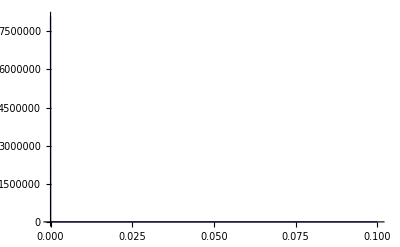

```mathematica
Plot[10^(13)*fgamfullfree[2*10^8]*grandgennew[Pi/2,w,2,2*10^8,bgaussvalue],{w,0,0.1}]
```

```mathematica
grandgennew[Pi/2,0.00000000001,2,2*10^8,bgaussvalue]
```

1.55235×10^-22

```mathematica
jgen[0.1,2.0,bgaussvalue]
```

1.0844664298231×10^-142251

```mathematica
jclass0raw[bgaussvalue]
```

0.0126776

```mathematica
xi[0.1,2,bgaussvalue]
```

327563.

```mathematica
Dmu[0.1,2,bgaussvalue]
```

0.00136996

```mathematica
sigma[0.1,2]
```

0.00485313

```mathematica
chi[0.1,2]
```

0.0358876

```mathematica
jgen[0.1,2,bgaussvalue]
```

1.0844664298231×10^-142251

```mathematica
ib1[327563.0]
```

$Aborted

```mathematica
NIntegrate[BesselK[5/3,x],{x,1,Infinity}]
```

0.651423

```mathematica
ib1[1]
```

0.651423

0.15081795142536965673

```mathematica
mybgaussvalue=Solve[Brat[b]==0.01,b][[1,1,2]]
```

4.41428×10^11

```mathematica
ib1[2.0]
xi[0.1,2,mybgaussvalue]
IB1[0.1,2,mybgaussvalue]
sigma[0.1,2]
chi[0.1,2]
Dmu[0.1,2,mybgaussvalue]
B2[0.1,2,mybgaussvalue]
B3[0.1,2,mybgaussvalue]
Kstuff[0.1,2,mybgaussvalue]
jgen[0.1,2,mybgaussvalue]
```

0.15081795142536965673

2.09754

0.13264578319999216183

0.00485313

0.0358876

0.541378

0.000535773

0.00370876

0.129473

2.98924×10^9

$Aborted

```mathematica
jclassthermalnew[rhobrad,10^(10),bgaussrad,2.658932568090915203094482421875`39.4247073235379*^9]
```

38839.3

```mathematica
(* OTHER TESTS *)
```

```mathematica
setupvalues;
setupiterguesses;
doprintdebug=1
```

```mathematica
Precision[c]
```

30.

1

```mathematica
eqtotdiff[T_,npairs_]:=eq1diff[T,npairs]^2+eq2diff[T,npairs]^2;
llleqtotdiff[lT_,lnpairs_]:=Log[10,eqtotdiff[10^lT,10^lnpairs]];
eqtotdiffstep[T_,npairs_]:=Module[{foo,var1,var2},var1=eq1diff[T,npairs];var2=eq2diff[T,npairs];If[var1>0&&var2>0,1,If[var1>0&&var2<0,2,If[var1<0&&var2>0,3,4]]]];
```

```mathematica
eqtotdiff[10^(10),10^(8)]
llleqtotdiff[10,8]
```

3.215597695262×10^6

6.50726170871545

```mathematica
NMinimize[eqtotdiff[x,y],{x,y}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate will be suppressed during this calculation.

{1.96929×10^-32,{x→3.89985×10^8,y→1.00438×10^11}}

```mathematica
FindMinimum[eqtotdiff
```

```mathematica
Plot3D[eqtotdiffstep[10^lT,10^lnpairs],{lT,7,11},{lnpairs,6,13}]
```

-Graphics3D-

```mathematica
Plot3D[eq1diff[10^lT,10^lnpairs],{lT,7,11},{lnpairs,6,13}]
```

-Graphics3D-

```mathematica
Plot3D[eq2diff[10^lT,10^lnpairs],{lT,7,11},{lnpairs,6,13}]
```

-Graphics3D-

```mathematica
eq1diff[10^9,10^12]
eq1diff[10^8,10^8]
```

2325.96

-0.999963

```mathematica
Plot3D[llleqtotdiff[lT,lnpairs],{lT,7,11},{lnpairs,6,13}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate will be suppressed during this calculation.

-Graphics3D-

```mathematica
Plot3D[llleqtotdiff[lT,lnpairs],{lT,8,9.5},{lnpairs,6,13}]
```

-Graphics3D-

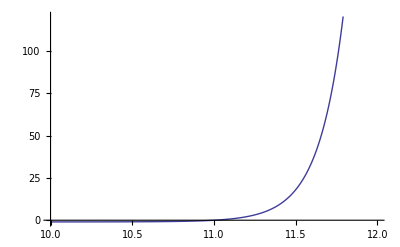

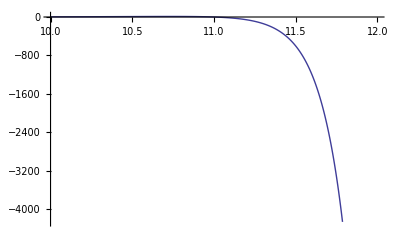

```mathematica
Plot[eq1diff[SetPrecision[10^(8.59125),40],10^ln],{ln,10,12},PlotPoints->1000]
Plot[eq2diff[SetPrecision[10^(8.59125),40],10^ln],{ln,10,12},PlotPoints->1000]
```

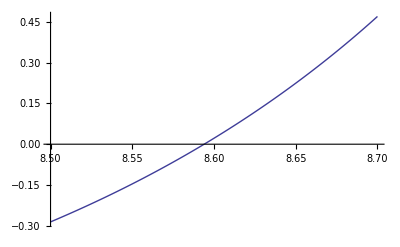

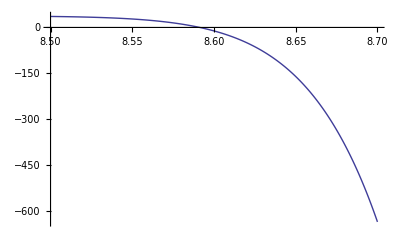

```mathematica
Plot[eq1diff[10^lT,10^(11)],{lT,8.5,8.7},PlotPoints->1000]
Plot[eq2diff[10^lT,10^(11)],{lT,8.5,8.7},PlotPoints->1000]
```

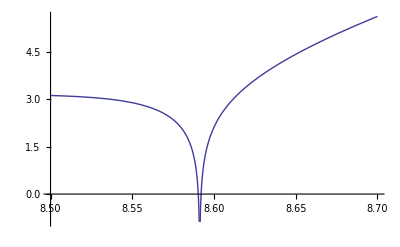

```mathematica
Plot[llleqtotdiff[lT,11],{lT,8.5,8.7},PlotPoints->1000]
```

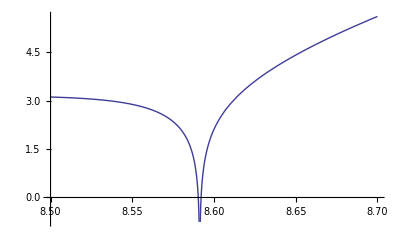

```mathematica
Plot[llleqtotdiff[lT,11],{lT,8.5,8.7}]
```

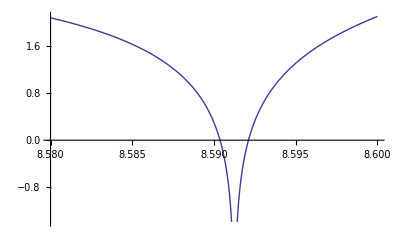

```mathematica
Plot[llleqtotdiff[lT,11],{lT,8.58,8.6}]
```

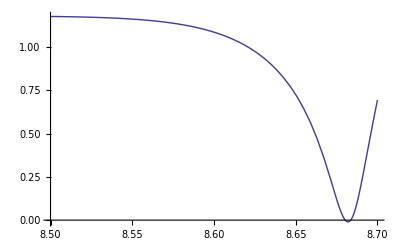

```mathematica
Plot[llleqtotdiff[lT,10],{lT,8.5,8.7}]
```

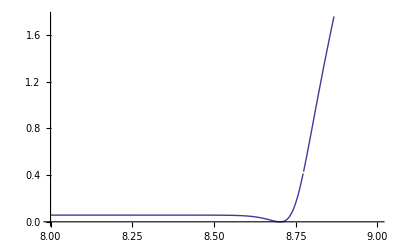

```mathematica
Plot[llleqtotdiff[lT,9],{lT,8.0,9.0}]
```

```mathematica
llleqtotdiff[8.59125,11]
```

-4.0198

```mathematica
llleqtotdiff[8.69,9]
```

0.00306252

0

```mathematica
setupvalues;
setupiterguesses;
doprintdebug=1
```

1

```mathematica
lowestprec
slowprec
```

30

15

```mathematica
(* get general functions *)
(*lowestprec=30;*)
lowestprec=MachinePrecision;
slowprec=MachinePrecision;
(*slowprec=MachinePrecision;*)
getPUNQ[];
```

```mathematica
var10=10^(8.59125);
var20=10^(11.0);

var10=3.1622*10^8;
var20=10^10;

rhobnorm=SetPrecision[rhobnorm,40];
rhobrat=SetPrecision[rhobrad,40];
Tnorm=SetPrecision[var10,40];
Trad=SetPrecision[Tnorm,40];
bgaussnorm=SetPrecision[bgaussnorm,40];
bgaussrad=SetPrecision[bgaussrad,40];
npairsnorm=SetPrecision[var20,40];
npairsrad=SetPrecision[npairsnorm,40];
Unprotect[Pgfunc];
Pgfunc[T_,npairs_]:=Pg[rhobnorm,rhobrad,T,bgaussnorm,bgaussrad,npairs]//.consts;
Protect[Pgfunc];
Pgnum=Pm; 

(* force balance condition *)
Unprotect[eq1diff,eq2diff];
Clear[eq1diff,eq2diff];
(* both are relative differences and reasonably normalized, but when lots of pairs, using $n_e$ to normalize might be too much of a constraint to have a relative error much less than unity *)
eq1diff[T_,npairs_]:=(Pgfunc[T,npairs]-Pgnum)/Pgnum//.consts;
eq2diff[T_,npairs_]:=(npairs-npairsfunc[rhobrad,T,bgaussrad,npairs])/(ne[rhobrad])//.consts;
Protect[eq1diff,eq2diff];

debugformat=0;
fulleq1[var1_?NumericQ,var2_?NumericQ]:=SetPrecision[Expand[eq1diff[var1,var2]],lowestprec];
fulleq2[var1_?NumericQ,var2_?NumericQ]:=SetPrecision[Expand[eq2diff[var1,var2]],lowestprec];

var10=Trad;
var20=npairsrad;

(* random error *)
erroreq1=Abs[fulleq1[var10,var20]];
erroreq2=Abs[fulleq2[var10,var20]];

(*{sols0,stxy}=Reap[FindRoot[{fulleq1[var1,var2]==0,fulleq2[var1,var2]==0},{{var1,var10},{var2,var20}},WorkingPrecision->lowestprec,EvaluationMonitor:>Sow[{var1,var2}]]];*)
(*{sols0,stxy}=Reap[FindRoot[{fulleq1[var1,var2]==0,fulleq2[var1,var2]==0},{{var1,var10},{var2,var20}},WorkingPrecision->lowestprec,StepMonitor:>Sow[{var1,var2}]]];*)

Print["Before FindRoot"];
supersols=Module[{s=0,e=0,var1,var2},
{sols0,{stxy}}=Reap[FindRoot[{fulleq1[var1,var2]==0,fulleq2[var1,var2]==0},{{var1,var10},{var2,var20}},WorkingPrecision->MachinePrecision,EvaluationMonitor:>{e++,Sow[{var1,var2,fulleq1[var1,var2],fulleq2[var1,var2]}]},StepMonitor:>{s++,Sow[{var1,var2,fulleq1[var1,var2],fulleq2[var1,var2]}]}]];
{sols0,"Steps"->s,"Evaluations"->e}
];
Print["After FindRoot"];
var10=sols0[[1,2]];
var20=sols0[[2,2]];

erroreq1=Abs[fulleq1[var10,var20]]
erroreq2=Abs[fulleq2[var10,var20]]

(*Module[{s=0,e=0},{FindRoot[ArcTan[1000Cos[x]],{x,1,2},Method->"Secant",StepMonitor:>s++,EvaluationMonitor:>e++],
"Steps"->s,"Evaluations"->e}]*)
```

Before FindRoot

NIntegrate::inumri: The integrand (-4.655597933811337`*^-63 - 1.4013944683091038`*^-24 ⅈ) ⅇ^44.342396644439404` gammap$155339 √1 - 1/gammap$155339^2 gammap$155339^2 Csc[thetap$155339] (-1 + gammap$155339^2 Sin[thetap$155339]^2) has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{5.848514355525109`*^-15, 3.611092824636958`*^-9}, {0.`, 0.9375`65.954589770191}}.

General::stop: Further output of NIntegrate will be suppressed during this calculation.

$Aborted

After FindRoot

$Aborted

3.68065

```mathematica
supersols
```

{{var1$134162→5.12474×10^8,var2$134162→1.03131×10^10},Steps→1,Evaluations→13}

```mathematica
stxy
```

{{3.1622×10^8,2.×10^11,3.08237919189022457899795881531,65.9802550934547440419919439591},{3.1622×10^8,2.×10^11,3.08237919189022457899795881531,65.9802550934547440419919439591},{3.1622×10^8,2.×10^11,3.08237928488715740016345989716,65.9802527824474793760600732639},{3.1622×10^8,2.×10^11,3.0823793505787819846375441557,65.980255855198819858742353972},{4.03687×10^8,1.09692×10^11,0.306783696651695414470140121921,-32.0615110948540547042284742929},{4.03687×10^8,1.09692×10^11,0.306783696651695414470140121921,-32.0615110948540547042284742929},{4.03687×10^8,1.09692×10^11,0.306783696651695414470140121921,-32.0615110948540547042284742929},{4.03687×10^8,1.09692×10^11,0.306783727062590605427772061375,-32.061525036526923315705062123},{4.03687×10^8,1.09692×10^11,0.30678374408346220647558766359,-32.061513141286880568259221036},{3.9472×10^8,1.00682×10^11,0.0250357866459518102475456657885,-6.68520360236981225909858039813},{3.9472×10^8,1.00682×10^11,0.0250357866459518102475456657885,-6.68520360236981225909858039813},{3.9472×10^8,1.00682×10^11,0.0250357866459518102475456657885,-6.68520360236981225909858039813},{3.9472×10^8,1.00682×10^11,0.0250358105192906507663330728519,-6.68521229647591042066778754815},{3.9472×10^8,1.00682×10^11,0.025035823486317124175748460857,-6.6852046393551862735193935805},{3.90335×10^8,1.00388×10^11,0.00020092414652721427427255196374,-0.425721746687501512163009920187},{3.90335×10^8,1.00388×10^11,0.00020092414652721427427255196374,-0.425721746687501512163009920187},{3.90335×10^8,1.00388×10^11,0.00020092414652721427427255196374,-0.425721746687501512163009920187},{3.90335×10^8,1.00388×10^11,0.000200947429386316473061413478973,-0.425729293147343368364232674139},{3.90335×10^8,1.00388×10^11,0.000200960087764909218566514170767,-0.425722556115418038213960016947},{3.89986×10^8,1.00437×10^11,-8.16523432912543763200667948365×10^-7,-0.00172400367133414820532133493458},{3.89986×10^8,1.00437×10^11,-8.16523432912543763200667948365×10^-7,-0.00172400367133414820532133493458},{3.89986×10^8,1.00437×10^11,-8.16523432912543763200667948365×10^-7,-0.00172400367133414820532133493458},{3.89986×10^8,1.00437×10^11,-7.93246609273803261541202838658×10^-7,-0.00173147762288845623833422049387},{3.89986×10^8,1.00437×10^11,-7.80586821320142388509516657991×10^-7,-0.00172479835560405232383618390202},{3.89985×10^8,1.00438×10^11,-1.77567954479248092513984033734×10^-11,-2.71246344183746946124472052431×10^-8},{3.89985×10^8,1.00438×10^11,-1.77567954479248092513984033734×10^-11,-2.71246344183746946124472052431×10^-8},{3.89985×10^8,1.00438×10^11,-1.77567954479248092513984033734×10^-11,-2.71246344183746946124472052431×10^-8},{3.89985×10^8,1.00438×10^11,2.32590801646245713559303273455×10^-8,-7.50078739490370966576555933347×10^-6},{3.89985×10^8,1.00438×10^11,3.59188981812913280616085054744×10^-8,-8.21749663828309553463287006475×10^-7},{3.89985×10^8,1.00438×10^11,3.60035998903573823459689645401×10^-16,-9.18190359281718198879952070877×10^-14},{3.89985×10^8,1.00438×10^11,3.60035998903573823459689645401×10^-16,-9.18190359281718198879952070877×10^-14}}

```mathematica
var10=Trad;
var20=npairsrad;
erroreq1=Abs[fulleq1[var10,var20]]
erroreq2=Abs[fulleq2[var10,var20]]
```

0.00975259643343994418507367603495

0.000655609747085681904047124332612

```mathematica
Trad
npairsrad
```

3.9016651994762742519378662109375×10^8

1.×10^11

```mathematica
erroreq1
erroreq2
```

Abs[fulleq1[sols0⟦1,2⟧,sols0⟦2,2⟧]]

Abs[fulleq2[sols0⟦1,2⟧,sols0⟦2,2⟧]]

```mathematica
slowprec=15
```

15

```mathematica
supersols
```

{{var1$97545→3.899849480228555038000560775317224468291×10^8,var2$97545→1.004375991177803722182116168564271256916×10^11},Steps→3,Evaluations→16}

```mathematica
sols0
```

{var1$87641→3.899849480229322582777346682208367743739×10^8,var2$87641→1.004375991180119626493462721176565710581×10^11}

```mathematica
fulleq1[3.901665199476274251937`40.*^8,1.`40.*^11]-fulleq1[3.901665199476274251976`40.*^8,1.`40.*^11]
```

-1.54638198006574681938656903953×10^-20

```mathematica
fulleq1[3.9016611112222333`40.*10^8,1.`40.*^11]-fulleq1[3.901661111222232`40.*10^8,1.`40.*^11]
fulleq1[3.9016611112222333`40.*10^8,1.`40.*^11]-fulleq1[3.9016611112222330`40.*10^8,1.`40.*^11]
fulleq1[3.9016611112222333`40.*10^8,1.`40.*^11]-fulleq1[3.9016611112222333`40.*10^8,1.`40.*^11]
```

9.00321484031962881999788805842×10^-16

0.

0.

```mathematica
eq1diff[3.9016611112222333`40.*10^8,1.`40.*^11]-eq1diff[3.901661111222232`40.*10^8,1.`40.*^11]
eq1diff[3.9016611112222333`40.*10^8,1.`40.*^11]-eq1diff[3.9016611112222330`40.*10^8,1.`40.*^11]
eq1diff[3.9016611112222333`40.*10^8,1.`40.*^11]-eq1diff[3.9016611112222333`40.*10^8,1.`40.*^11]
```

9.00321×10^-16

0.

0.

```mathematica
Precision[eq1diff[3.9016611112222333`40.*10^8,1.`40.*^11]]
Precision[eq2diff[3.9016611112222333`40.*10^8,1.`40.*^11]]
```

MachinePrecision

MachinePrecision

```mathematica
Precision[rhobnorm]
Precision[rhobrad]
Precision[Tnorm]
Precision[bgaussnorm]
Precision[bgaussrad]
Precision[npairsrad]
```

40.

30.

40.

40.

40.

«1 more identical outputs»

```mathematica
Precision[Pgfunc[3.9016611112222333`40.*10^8,1.`40.*^11]]
Precision[Pg[rhobnorm,rhobrad,Tnorm,bgaussnorm,bgaussrad,npairsrad]]
Precision[Prad[rhobrad,Tnorm,bgaussrad,npairsrad]]
Precision[Ppairs[rhobrad,Tnorm,bgaussrad,npairsrad]]

Precision[Pbaryon[rhobrad,Tnorm]]
Precision[Pe[rhobrad,Tnorm]]
Precision[Pnu[rhobrad,Tnorm,bgaussrad,npairsrad]];
Precision[Pgnum]
Precision[consts]
```

MachinePrecision

MachinePrecision

MachinePrecision

«1 more identical outputs»

30.

30.

30.

«1 more identical outputs»

```mathematica
Precision[urad0[Tnnorm]]
Precision[damptaurad[rhobrad,Tnorm,bgaussrad,npairsrad]]
```

30.

MachinePrecision

```mathematica
Precision[tauradsca[rhobrad,Tnorm,bgaussrad,npairsrad]]
Precision[tauradtot[rhobrad,Tnorm,bgaussrad,npairsrad]]
Precision[tauradabs[rhobrad,Tnorm,bgaussrad,npairsrad]]
```

30.

MachinePrecision

MachinePrecision

```mathematica
Precision[sigmaes[Tnorm,bgaussrad]]
Precision[Nscalayers*Lpnum]
Precision[ ne[rhobrad]]
Precision[Rjet//.consts]
```

30.

30.

30.

«1 more identical outputs»

```mathematica
Precision[dtauradabsds[rhobrad,Trad,bgaussrad,npairsrad]]
Precision[nb[rhobrad]]
Precision[Nabslayers*Lpnum+ne[rhobrad]*Rjet]
```

MachinePrecision

30.

30.

```mathematica
Precision[nbsigmaff[rhobrad,Trad,bgaussrad,npairsrad]]
Precision[nbsigmasynch[rhobrad,Trad,bgaussrad,npairsrad]]
```

30.

MachinePrecision

```mathematica
Precision[Bc]
```

30.

```mathematica
Precision[jgeo]
Precision[rawcoef]
Precision[jclass0raw[bgaussrad]]
Precision[jclass0[2,bgaussrad]]
Precision[jclassnew[Pi/2,2,bgaussrad]]
Precision[grandit[Pi/2,2,Trad,bgaussrad]]
```

40.

40.

30.

30.

30.

«1 more identical outputs»

```mathematica
jclassthermalneworig[rhobrad,Trad,bgaussrad,npairsrad]
```

$Aborted

```mathematica
NIntegrate[grandit[thetap,gammap,Trad,bgaussrad],{thetap,0,Pi},{gammap,1/Sin[thetap],Infinity}]
Precision[%]
```

1.70505×10^-8

MachinePrecision

```mathematica
netot2[rhobrad,npairsrad]*NIntegrate[grandit[thetap,gammap,Trad,bgaussrad],{thetap,0,Pi},{gammap,1/Sin[thetap],Infinity},WorkingPrecision->30]
Precision[%]
```

$Aborted

∞

```mathematica
jclassthermalnew[rhobrad,Trad,bgaussrad,npairsrad]
jclassthermalnew[rhobrad,Trad,bgaussrad,npairsrad]
```

4900.06491812460991933465845714

```mathematica
rhobrad
Trad
bgaussrad
```

8.83052876594752663300784526581×10^-15

3.9016651994762742519378662109375×10^8

11402.81371332414164498914033174514770508

```mathematica
god=NIntegrate[Sin[Sin[x]],{x,0,2},WorkingPrecision->30]
Precision[god]
```

1.24705605824400292488389213407

30.

```mathematica
Precision[fulleq1[3.9016611112222333`40.*10^8,1.`40.*^11]]
```

37.9892

```mathematica
Precision[c]
```

MachinePrecision

```mathematica
c
```

```mathematica
Precision[c]
```

MachinePrecision

```mathematica
$MinPrecision
```

30

```mathematica
lowestprec
```

30

```mathematica
6``{lowestprec}
```

```mathematica
Max[5,6]
```

6

```mathematica
c=2.99792458*10^(10) ;
Precision[c]
```

MachinePrecision

```mathematica
Clear[c]
```

```mathematica
getconstants
```

```mathematica
stxy
```

```mathematica
Plot3D[eqtotdiff[T,npairs],{T,10^7,10^10},{npairs,10^6,10^13}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

-Graphics3D-